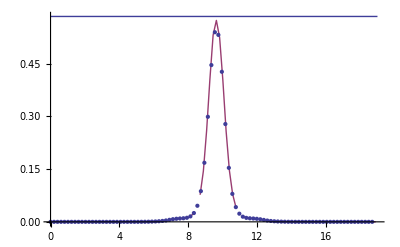

```mathematica
Get["./dirtest/comp1.m"];
Get["./dirtest/vEff1.m"];
Get["./dirtest/rho1.m"];
Get["./dirtest/drho1.m"];
Get["./dirtest/compensation1.m"];
Get["./dirtest/vzero1.m"];
Get["./dirtest/xc1.m"];
Show[ListPlot[{densityScreened,qdeltarho},Joined->{False,True},PlotRange->All],Plot[qmaxs[[2]],{z,0,19}]]
```

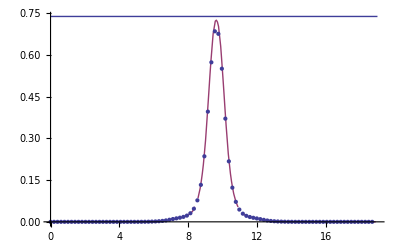

```mathematica
Show[ListPlot[{density,qrho},Joined->{False,True},PlotRange->All],Plot[qmaxs[[1]],{x,0,19}]]
```

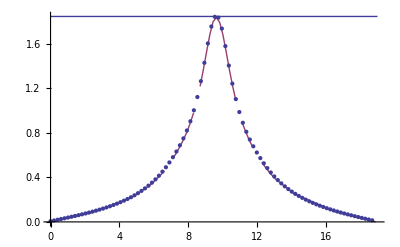

```mathematica
Show[ListPlot[{vEff,qvEff},Joined->{False,True},PlotRange->All],Plot[qmaxs[[3]],{x,0,19}]]
```

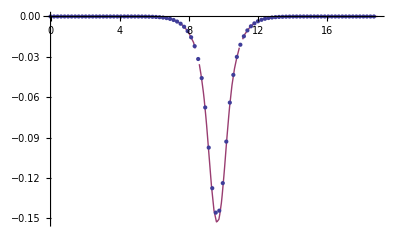

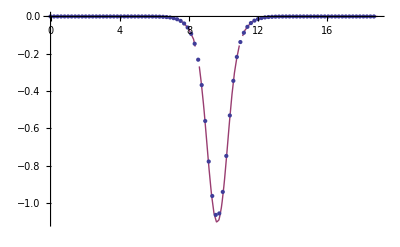

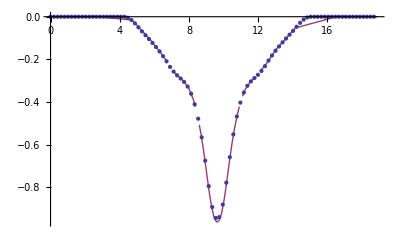

```mathematica
ListPlot[{CompensationCharge,qCompensationCharge},Joined->{False,True},PlotRange->All]
ListPlot[{VZero,qVzero},Joined->{False,True},PlotRange->All]
ListPlot[{XC,qXC},Joined->{False,True},PlotRange->All]
```

```mathematica
Length[vEff]
```

60

```mathematica
114/75.
```

1.52

```mathematica
fvEff=Interpolation[vEff]
```

InterpolatingFunction[{{0.,18.7315}},<>]

```mathematica
4π NIntegrate[z^2*fvEff[z+18.7315/2],{z,0,18.7315/2}]
```

475.848

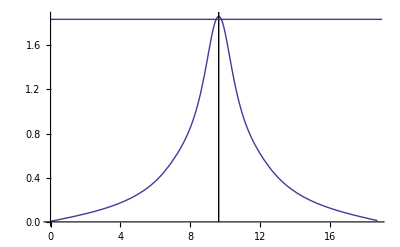

```mathematica
Show[Plot[fvEff[z],{z,0,18.7315}],Graphics[Line[{{9.634807747143459,0},{9.634807747143459,2}}]],Plot[1.83543,{z,0,19}]]
```

```mathematica
FindMaximum[fvEff[z],{z,0,18.73}]
```

{1.86171,{z→9.63481}}

```mathematica
4π NIntegrate[z^2*fvEff[-z+9.634807747143459],{z,0,9.634807747143459}]
```

441.198

```mathematica
18.7315/2
```

9.36575

```mathematica
Integrate[Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

4 π

```mathematica
￿
```